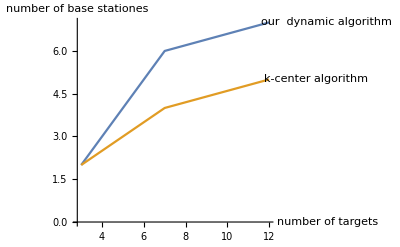

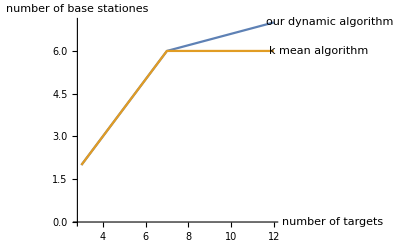

```mathematica
SetDirectory[NotebookDirectory[]];
 text=Import["log.txt"];

 t=StringSplit[text,"
"];
matrix={};



For[i=1,i<Length[t],i++,
AppendTo[matrix,StringSplit[t[[i]],","]];
]

myg={};
kcenterg={};
kmean={};
For[i=1,i<Length[t],i++,
AppendTo[myg,{Interpreter["Number"][matrix[[i]][[1]]],Interpreter["Number"][matrix[[i]][[2]]]}];
AppendTo[kcenterg,{Interpreter["Number"][matrix[[i]][[1]]],Interpreter["Number"][matrix[[i]][[3]]]}];
AppendTo[kmean,{Interpreter["Number"][matrix[[i]][[1]]],Interpreter["Number"][matrix[[i]][[4]]]}];
]
ListLinePlot[{Labeled[myg,"our  dynamic algorithm"],Labeled[kcenterg,"k-center algorithm"]},AxesLabel -> {"number of targets", "number of base stationes"}]
ListLinePlot[{Labeled[myg,"our dynamic algorithm"],Labeled[kmean,"k mean algorithm"]},AxesLabel -> {"number of targets", "number of base stationes"}]
```

{}

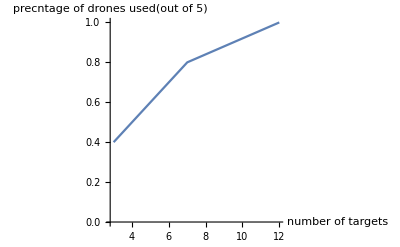

```mathematica
log2=Import["log2.txt"];
 percordstring=StringSplit[log2,"
"];

prcetNumber={}


For[i=1,i<Length[percordstring],i++,
temp=StringSplit[percordstring[[i]],","];
AppendTo[prcetNumber,{Interpreter["Number"][temp[[1]]],Interpreter["Number"][temp[[2]]]}];
]

ListLinePlot[prcetNumber,AxesLabel ->{"number of targets","Percentage of drones used(out of 5)"}]
```